## Метод k ближайших соседей

### Модельные данные

1. В качестве модельных данных возьмите точки из двух двумерных нормальных распределений с разными математическими ожиданиями и дисперсиями, представленными в таблице. Сгенерируйте обучающую и тестовую выборки для каждого из случаев. Для тестирования возьмите 30 объектов.

```mathematica
Grid[{Style[#,Bold]&/@{" ","μ_1","σ_1^2","n_1","μ_2","σ_2^2","n_2"},{1,0,4,60,20,4,50},{2,0,4,60,5,4,50},{3,0,4,60,0,12,50}},Frame->All,Background->{{LightBlue},{LightBlue}},Spacings->{1.5,1.5},ItemStyle->Directive[FontSize->16]]
```

| μ_1 | σ_1^2 | n_1 | μ_2 | σ_2^2 | n_2
1 | 0 | 4 | 60 | 20 | 4 | 50
2 | 0 | 4 | 60 | 5 | 4 | 50
3 | 0 | 4 | 60 | 0 | 12 | 50

В первом случае мы имеем дело с хорошо разделимой выборкой. Во втором случае классы сближены. В третьем математические ожидания классов совпадают, но различаются дисперсии.

Используйте функции RandomVariate и NormalDistribution. Изобразите точки на трех графиках, соответствующих каждому из случаев.

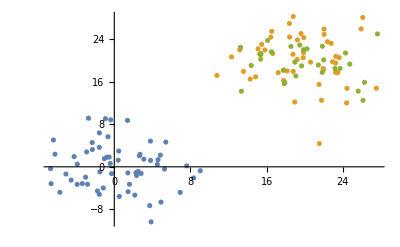

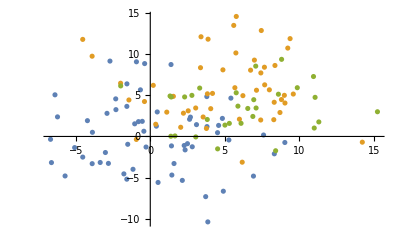

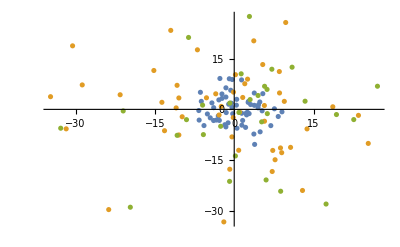

```mathematica
(* Ваш код здесь *)
class1= RandomVariate[NormalDistribution[0,4],{60,2}];
class21 = RandomVariate[NormalDistribution[20,4],{50,2}];
class22= RandomVariate[NormalDistribution[5,4],{50,2}];
class23 = RandomVariate[NormalDistribution[0,12],{50,2}];
test1 := RandomVariate[NormalDistribution[20,4],{30,2}];
test2 := RandomVariate[NormalDistribution[5,4],{30,2}];
test3:=RandomVariate[NormalDistribution[0,12],{30,2}];


ListPlot[{class1,class21,test1}]
ListPlot[{class1,class22,test2}]
ListPlot[{class1,class23,test3}]
```

### Выбор числа соседей

Метод k ближайших соседей состоит в попарном сравнении новых объектов с объектами обучающей выборки с помощью некоторой метрики.

2. Используйте в качестве метрики евклидово расстояние между точками. Решите задачу методом k ближайших соседей при 3 различных значениях параметра k. Сравните полученные результаты на тестовой выборке и сделайте выводы.

```mathematica
(* Ваш код здесь *)


kNN[cl1_,cl2_,testSet_,k_]:=Table[MaximalBy[Tally[SortBy[Join[Table[{EuclideanDistance[cl1[[i]],test],1},{i,Length[cl1]}],Table[{EuclideanDistance[cl2[[j]],test],2},{j,Length[cl2]}]],First][[;;k]][[All,2]]],2][[1,1]],{test,testSet}];

case11 =kNN[class1,class21,test1,1]
case12 =kNN[class1,class21,test1,3]
case13 =kNN[class1,class21,test1,5]
case21 =kNN[class1,class22,test2,1]
case22 =kNN[class1,class22,test2,5]
case23 =kNN[class1,class22,test2,11]
case31 =kNN[class1,class23,test3,1]
case32 =kNN[class1,class23,test3,5]
case33 =kNN[class1,class23,test3,13]
Cases[Join[Tally[case11],Tally[case12],Tally[case13],Tally[case21],Tally[case22],Tally[case23],Tally[case31],Tally[case32],Tally[case33]],{2,_}][[All,2]]*100/30//N(*Процент верно классифицированных объектов из тестовой выборки для каждого случая при трех разных количестве соседей*)
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

{2,1,1,2,2,2,1,1,2,2,1,1,2,2,1,1,1,1,1,1,2,1,2,2,2,2,2,2,2,2}

{2,2,1,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

{2,1,2,2,2,1,2,2,2,2,2,2,2,1,2,2,2,2,2,1,2,2,2,2,1,2,2,2,1,2}

{2,1,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

{100.,100.,100.,56.6667,93.3333,100.,80.,93.3333,100.}

## Метод Парзеновского окна

В задании предлагается сравнить качество полученных результатов при различных функциях ядра K(z).

Решение методом Парзеновского окна ищется в виде

a(x)=arg max_(y∈Y) ∑_(i=1)^l [y_i=y]K((ρ(x,x_i))/h),

где  K(z) – функция ядра, ρ(x,x_i) – расстояние между классифицируемым объектом и объектом выборки, а h – ширина окна.

Ядро может быть выбрано из нижеприведенного набора ядер:

```mathematica
Grid[{Style[#,Bold]&/@{" ","K(z)","формула"},
{1,"Епанечникова","E(z)=3/4(1-z^2)[|z| ≤ 1]"},
{2,"Квартическое","Q(z)=15/16(1-z^2)^2[|z| ≤ 1]"},
{3,"Треугольное","T(z)=(1-|z|)[|z| ≤ 1]"},
{4,"Гауссовское","G(z)=(2π)^(-FractionBox[1, 2])ⅇ^(-FractionBox[1, 2] SuperscriptBox[z, 2])"},
{5,"Прямоугольное","П(z)=1/2[|z| ≤ 1]"}},Frame->All,Background->{{LightBlue},{LightBlue}},Spacings->{1.5,1.5},ItemStyle->Directive[FontSize->16]]
```

| K(z) | формула
1 | Епанечникова | E(z)=3/4(1-z^2)[|z| ≤ 1]
2 | Квартическое | Q(z)=15/16(1-z^2)^2[|z| ≤ 1]
3 | Треугольное | T(z)=(1-|z|)[|z| ≤ 1]
4 | Гауссовское | G(z)=(2π)^(-FractionBox[1, 2])ⅇ^(-FractionBox[1, 2] SuperscriptBox[z, 2])
5 | Прямоугольное | П(z)=1/2[|z| ≤ 1]

### Выбор функции ядра

3. По исходным данным выберете ширину окна. Постройте классификаторы со всеми перечисленными функциями ядра.  Проведите эксперименты для каждого из случаев 50 раз и укажите среднее качество. Сделайте выводы.

```mathematica
(* Ваш код здесь *)
kern1[z_]:=3/4*(1-z^2);
kern2[z_]:=15/16*(1-z^2)^2
kern3[z_]:=(1-Abs[z])
kern4[z_]:= (2*Pi[])^(-1/2)*Exp^(-1/2*z^2)
kern5[z_]:=1/2;
Clear[ParzWin]
ParzWin [cls1_,cls2_,testSet_,h_,kern_]:=Table[MaximalBy[DeleteMissing[Join[Table[If[(EuclideanDistance[cls1[[i]],test]/h)>1,Missing[],{(EuclideanDistance[cls1[[i]],test]/h)//kern,1}],{i,Length[cls1]}],Table[If[EuclideanDistance[cls2[[j]],test]/h>1,Missing[],{(EuclideanDistance[cls2[[j]],test]/h)//kern,2}],{j,Length[cls2]}]]],1][[1,2]],{test,testSet}]

experiment[cl1_,cl2_,testSet_,h_,kern_]:=Module[{res=0},Do[res=res+Cases[Tally[ParzWin[cl1,cl2,testSet,h,kern]],{2,_}][[1,2]],{x,50}];Return[res/1500*100//N]]

exp1={experiment[class1,class21,test1,10,kern1],experiment[class1,class21,test1,10,kern2],experiment[class1,class21,test1,10,kern3],experiment[class1,class21,test1,10,kern4],experiment[class1,class21,test1,10,kern5]} (*Эксперименты для 1ого случая со всеми типами ядер*)
```

{100.,100.,100.,100.,100.}

```mathematica
exp2={experiment[class1,class22,test2,10,kern1],experiment[class1,class22,test2,10,kern2],experiment[class1,class22,test2,10,kern3],experiment[class1,class22,test2,10,kern4],experiment[class1,class22,test2,10,kern5]} (*Эксперименты для 2ого случая со всеми типами ядер*)
```

{73.3333,66.6667,76.6667,73.3333,100.}

```mathematica
exp3={experiment[class1,class23,test3,20,kern1],experiment[class1,class23,test3,20,kern2],experiment[class1,class23,test3,20,kern3],experiment[class1,class23,test3,20,kern4],experiment[class1,class23,test3,20,kern5]} (*Эксперименты для 3ого случая со всеми типами ядер*)
```

{56.6667,76.6667,73.3333,86.6667,100.}